```mathematica
SetOptions[$FrontEnd,"CommonDefaultFormatTypes"->{"Output"->StandardForm}]
basepath=$HomeDirectory<>"/sivers_TMD_PhD_project/mathematica_hari"
SetDirectory[basepath<>"/output"];
includepath=basepath<>"/include";
AppendTo[$Path, includepath];
Needs["LatticeAnalysis`"];
 <<"LatticeAnalysis`"
(* do not keep track of intermediate results *)
$HistoryLength=0;
Needs["FourierSeries`"]
lata=0.11403
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/mathematica_hari

0.11403

## Open Database

```mathematica
AmpDB = BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/newDBforA12BA2B/db_Alleta_correct_try_A12B_A2B_bL_bT_bevenodd.bidatex"]
```

< -MemDB- {A,bL,bNum,bT,data,EN,etav,MN,PL,zta}>

```mathematica
modelfitJackkife[model_, fitParams_, x_, y_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,y,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
meanfromJK[JKvalue_]:=Module[{meanvalue},
meanvalue = MakeErrBars[{{1,JKvalue}}][[1]][[1]][[2]];
meanvalue
];
errorfromJK[JKvalue_]:=Module[{errorvalue},
errorvalue = MakeErrBars[{{1,JKvalue}}][[1]][[2]][[1]][[2]];
errorvalue
];
chisqOEsigmasq[O_, E_]:=Module[{OEsigmasq, Omean,Emean, Esigmasq, Osigmasq, sigmasqTotal},
Omean=meanfromJK[O];
Emean=meanfromJK[E];
Esigmasq = (MakeErrBars[{{1,E}}][[1]][[2]][[1]][[2]])^2;
Osigmasq = (MakeErrBars[{{1,O}}][[1]][[2]][[1]][[2]])^2;
sigmasqTotal = Esigmasq+Osigmasq;
OEsigmasq = If[sigmasqTotal==0,0,((Omean-Emean)^2)/sigmasqTotal];
OEsigmasq
];

JackknifeFit3D[xyJKf_,model_,para_,vari_, modelFnName_]:=Module[
{numFs,fitParamsForFj,fitParamsList,paramLists,jackknifeResults,DoF, chisquare, observed, expected, chisquareperDoF},
numFs=Length[xyJKf[[1,3]]];
WeightList = {};
Do[
ε=10^-6;
σ=(MakeErrBars[{{1,xyJKf[[ii]][[3]]}}][[1]][[2]][[1]][[2]]);
AppendTo[WeightList,1/Max[σ,ε]^2], {ii, Length[xyJKf]}];
(*Function to extract j-th f values and fit them*)
fitParamsForFj[j_]:=Module[{data,fit},
data={#[[1]],#[[2]],#[[3,j]]}&/@xyJKf;(*Extract f_j values*)
fit=NonlinearModelFit[data,model,para,vari, Weights->WeightList,Method->{"LevenbergMarquardt"}];
fit["BestFitParameters"] (*Extract fitted parameters*)
];
(*Compute fit parameters for each f_j*)
fitParamsList=Table[fitParamsForFj[j],{j,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
DoF=Length[xyJKf];
chisquare=0;
Do[
observed = modelfitJackkife[modelFnName, jackknifeResults, xyJKf[[i]][[1]], xyJKf[[i]][[2]]];
expected= xyJKf[[i]][[3]];
chisquare = chisquare + chisqOEsigmasq[observed, expected];
,{i,DoF}];
chisquareperDoF=chisquare/(DoF-3);
{FitParameters->jackknifeResults, chisquareDoF->chisquareperDoF}];

modelfitJackkifband[model_, fitParams_,fixedVare_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x, fixedVare,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];

NFourierTransformJK[modelReA12BNfou_,pb_,x_, FourierNum_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->-1,etav->8, bNum->even}],MN][[1]]];
modelvalue=ParallelTable[FourierNum[NFourierTransform[modelReA12BNfou[pb, j],pb,x]],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];

modelfitJackkifex[model_, fitParams_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
modelfitJackkifex[model_, fitParams_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
```

```mathematica
SiversShift[b2_,P1_, etavalue_]:=Module[{dataforfitA12B, dataforfitA2B, fitJKA12B, fitParasA12B, chisqfitA12B, fitJKA2B, fitParasA2B, chisqfitA2B, fitJKImA2B, fitParasImA2B, chisqfitImA2B},
dataforfitA12B = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->P1,etav->etavalue, bNum->even}],{bL, bT,data}];
dataforfitA2B = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1,etav->etavalue, bNum->even}],{bL, bT,data}];
dataforfitImA2BFull = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1,etav->etavalue, bNum->odd}],{bL, bT,data}];
Print[" for  are all removed!"];
dataforfitA12B = Select[dataforfitA12B,Sqrt[#[[1]]^2+#[[2]]^2]>4&];
dataforfitA2B = Select[dataforfitA2B,Sqrt[#[[1]]^2+#[[2]]^2]>4&];
dataforfitImA2B = Select[dataforfitImA2BFull,Sqrt[#[[1]]^2+#[[2]]^2]>4&];
modelfitA12B[x1_,x2_,{a_,b_,c_}]:=a*(1/((x1^2)+b))*(1/((x2^2)+c));
modelfitA2B[x1_,x2_,{a_,b_,c_}]:=a*(1/((x1^2)+b))*(1/((x2^2)+c));
modelfitImA2B[x1_,x2_,{a_,b_,c_}]:=a*x1*(1/((x1^2)+b))*(1/((x2^2)+c));
fitJKA12B =JackknifeFit3D[dataforfitA12B,modelfitA12B[bP,bsq,{a,b,c}],{a,b, c},{bP,bsq}, modelfitA12B];
fitParasA12B=FitParameters/. fitJKA12B;
chisqfitA12B=chisquareDoF/. fitJKA12B;
fitJKA2B =JackknifeFit3D[dataforfitA2B,modelfitA2B[bP,bsq,{a,b,c}],{a,b, c},{bP,bsq}, modelfitA2B];
fitParasA2B=FitParameters/. fitJKA2B;
chisqfitA2B=chisquareDoF/. fitJKA2B;
fitJKImA2B =JackknifeFit3D[dataforfitImA2B,modelfitImA2B[bP,bsq,{a,b,c}],{a,b, c},{bP,bsq}, modelfitImA2B];
fitParasImA2B=FitParameters/. fitJKImA2B;
chisqfitImA2B=chisquareDoF/. fitJKImA2B;
Print["Fitting:    -> () = ",OutputForm[fitParasA12B], ", chisquareDoF = ", chisqfitA12B,"\n Fitting:    -> () = ",OutputForm[fitParasA2B], ", chisquareDoF = ", chisqfitA2B, "\n Fitting:   -> () = ",OutputForm[fitParasImA2B]," chisquareDoF = ", chisqfitImA2B, "\n  = ",b2, "  = ",P1," ,eta = ", etavalue];
b2II = b2*fitParasA12B[[1]]/fitParasA12B[[1]];
II= fitParasA12B[[1]]/fitParasA12B[[1]];
fitaA12B =fitParasA12B[[1]];
fitbA12B=fitParasA12B[[2]];
fitcA12B =fitParasA12B[[3]];
fitaA2B =fitParasA2B[[1]];
fitbA2B=fitParasA2B[[2]];
fitcA2B =fitParasA2B[[3]];
fitaImA2B =fitParasImA2B[[1]];
fitbImA2B=fitParasImA2B[[2]];
fitcImA2B =fitParasImA2B[[3]];
MassN = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->P1,etav->etavalue, bNum->even}],MN][[1]];
(*reducedratioA12B=(fitaA12B/(fitcA12B+b2II))*(II/(2*fitbA12B));
fourierA12B[x_, {reducedr_, bA12B_, cA12B_}] :=Sech[((N[Pi]*x)/(2*bA12B))]*reducedr;
reducedratioA2B=(fitaA2B/(fitcA2B+b2II))*(II/(2*fitbA2B));
reducedratioImA2B=(fitaImA2B/(fitcImA2B+b2II))*(II/(2*Sqrt[2]*(fitbImA2B)^(3/2)));
fourierA2B[x_, {reducedr_, bA2B_, bImA2B_}] :=Sech[((N[Pi]*x)/(2*bA2B))]*reducedr;
(*Print[reducedratioImA2B];*)
fourierImA2B[x_, {reducedr_, bA2B_, cA2B_}] :=x*Exp[-(x^2)/(4*bA2B)]*reducedr;
(*reducedratio1 = -MassN*(197*0.0001/lata)*reducedratioA12B/reducedratioA2B;
siversratio[x_, {reducedr1_, bA12B_, bA2B_}] := reducedr1*(Sech[((N[Pi]*x)/(2*bA12B))]/Sech[((N[Pi]*x)/(2*bA2B))]);*)*)
massterm=-MassN[[1]]*(197*0.0001/lata);
siversshiftxforplot={};
fourieA12Bxforplot={};
fourieA2Bxforplot={};
Do[
(*siversrforx = modelfitJackkifex[siversratio,{reducedratio1, fitbA12B, fitbA2B}, x];*)
modelReA12BNfou[pb_, jknum_]:=fitaA12B[[jknum]]*1/(fitbA12B[[jknum]]+((pb^2)/(P1^2)))*1/(fitcA12B[[jknum]]+(b2^2+((pb^2)/(P1^2))));
modelReA2BNfou[pb_, jknum_]:=fitaA2B[[jknum]]*1/(fitbA2B[[jknum]]+((pb^2)/(P1^2)))*1/(fitcA2B[[jknum]]+(b2^2+((pb^2)/(P1^2))));
modelImA2BNfou[pb_, jknum_]:=fitaImA2B[[jknum]]*((pb)/(-P1))*1/(fitbImA2B[[jknum]]+((pb^2)/(P1^2)))*1/(fitcImA2B[[jknum]]+(b2^2+((pb^2)/(P1^2))));
fourierA12Bforx = NFourierTransformJK[modelReA12BNfou,pb,x, Re];
fourierREA2Bforx=NFourierTransformJK[modelReA2BNfou,pb,x, Re];
fourierIMA2Bforx=NFourierTransformJK[modelImA2BNfou,pb,x, Im];
fourierA2Bforx=fourierREA2Bforx-fourierIMA2Bforx;
siversrforx=massterm*fourierA12Bforx/fourierA2Bforx;
AppendTo[siversshiftxforplot,{x,siversrforx}];
AppendTo[fourieA12Bxforplot,{x,fourierA12Bforx}];
AppendTo[fourieA2Bxforplot,{x,fourierA2Bforx}];
,{x,0,1, 0.2}];
MkErrA12B=MakeErrBars[fourieA12Bxforplot];
A12BPltrangMin=(MkErrA12B[[1]][[1]][[2]]+MkErrA12B[[1]][[2]][[1]][[1]])*0.5;
A12BPltrangMax=(MkErrA12B[[1]][[1]][[2]]+MkErrA12B[[1]][[2]][[1]][[2]])*1.5;
PlotfourieA12Bx = ErrorListPlot[MkErrA12B,FrameLabel->{ , }, Frame->True , PlotRange->{{Automatic,Automatic},{0,A12BPltrangMax}}];(* {{Automatic,Automatic},{0,0.0004}}*)
Print[PlotfourieA12Bx];
MkErrA2B=MakeErrBars[fourieA2Bxforplot];
A2BPltrangMin=(MkErrA2B[[1]][[1]][[2]]+MkErrA2B[[1]][[2]][[1]][[1]])*0.5;
A2BPltrangMax=(MkErrA2B[[1]][[1]][[2]]+MkErrA2B[[1]][[2]][[1]][[2]])*2;
PlotfourieA2Bx= ErrorListPlot[MkErrA2B,FrameLabel->{ , }, Frame->True , PlotRange->Full];(*{{Automatic,Automatic},{0.0045,0.0055}}*)
Print[PlotfourieA2Bx];
Print["Sivers shift in GeV"];
MkErrsiversshift=MakeErrBars[siversshiftxforplot];
SsPltrangMin=(MkErrsiversshift[[1]][[1]][[2]]-MkErrsiversshift[[1]][[2]][[1]][[1]])*0.5;
SsPltrangMax=(MkErrsiversshift[[1]][[1]][[2]]-MkErrsiversshift[[1]][[2]][[1]][[2]])*1.2;
Plotsivershift = ErrorListPlot[MkErrsiversshift,FrameLabel->{ , }, Frame->True , PlotRange->{{Automatic,Automatic},{0,0.1}}];(* PlotRange->{{Automatic,Automatic},{-0.3,0}}*)
Print[Plotsivershift];
(*Export["/Users/hariprashadravikumar/Downloads/Lorentz_bL_Lorentz_bT_Fourierx_A12B_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotfourieA12Bx,"PDF",ImageResolution->600];
Export["/Users/hariprashadravikumar/Downloads/Lorentz_bL_Lorentz_bT_Fourierx_A2B_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotfourieA2Bx,"PDF",ImageResolution->600];
Export["/Users/hariprashadravikumar/Downloads/Lorentz_bL_Lorentz_bT_Fourierx_SiversShift_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",Plotsivershift,"PDF",ImageResolution->600];*)
];
```

for  are all removed!

Fitting:    -> () = {⟨-0.29(11)⟩_(2902J), ⟨5.5(22)⟩_(2902J), ⟨1.9(11)⟩_(2902J)}, chisquareDoF = 0.814278
 Fitting:    -> () = {⟨1.84(14)⟩_(2902J), ⟨8.51(60)⟩_(2902J), ⟨5.82(43)⟩_(2902J)}, chisquareDoF = 8.29387
 Fitting:   -> () = {⟨0.115(34)⟩_(2902J), ⟨2.1(12)⟩_(2902J), ⟨7.1(27)⟩_(2902J)} chisquareDoF = 1.19191
  = 9  = -1 ,eta = 8

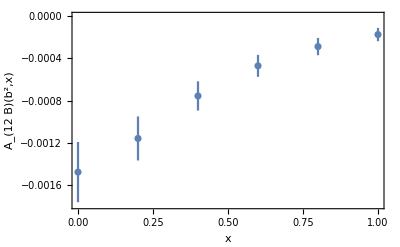

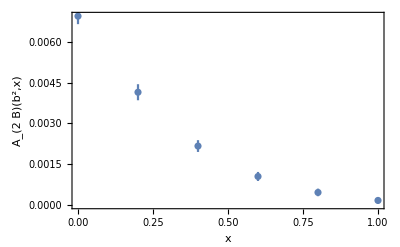

Sivers shift in GeV

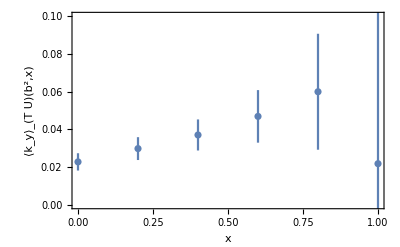

```mathematica
SiversShift[9,-1, 8]
```

for  are all removed!

Fitting:    -> () = {⟨-0.21(11)⟩_(2902J), ⟨6.1(30)⟩_(2902J), ⟨2.8(25)⟩_(2902J)}, chisquareDoF = 1.19978
 Fitting:    -> () = {⟨0.90(14)⟩_(2902J), ⟨6.23(96)⟩_(2902J), ⟨3.99(63)⟩_(2902J)}, chisquareDoF = 2.2664
 Fitting:   -> () = {⟨0.137(43)⟩_(2902J), ⟨2.1(14)⟩_(2902J), ⟨5.9(24)⟩_(2902J)} chisquareDoF = 0.808313
  = 9  = -2 ,eta = 8

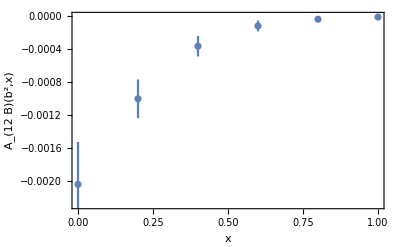

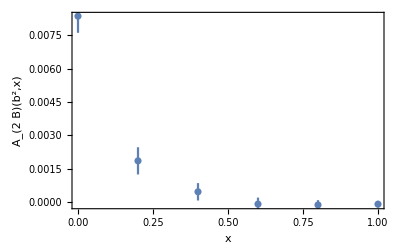

Sivers shift in GeV

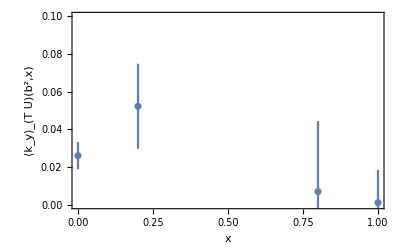

```mathematica
SiversShift[9,-2, 8]
```

for  are all removed!

Fitting:    -> () = {⟨-0.01 ± 0.15⟩_(2902J), ⟨2.2(72)⟩_(2902J), ⟨-3. ± 10.⟩_(2902J)}, chisquareDoF = 0.686905
 Fitting:    -> () = {⟨0.56(29)⟩_(2902J), ⟨5.8(23)⟩_(2902J), ⟨5.0(30)⟩_(2902J)}, chisquareDoF = 1.1293
 Fitting:   -> () = {⟨0.066(58)⟩_(2902J), ⟨1.4(37)⟩_(2902J), ⟨2.2(28)⟩_(2902J)} chisquareDoF = 0.237305
  = 9  = -3 ,eta = 8

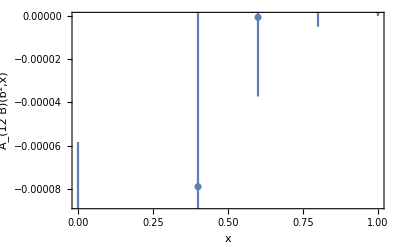

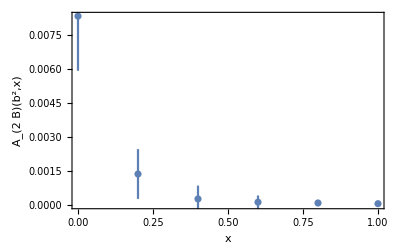

Sivers shift in GeV

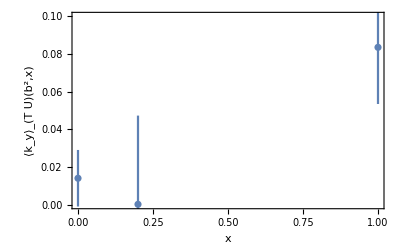

```mathematica
SiversShift[9,-3, 8]
```

```mathematica
SiversShift2[b2_,P1_, etavalue_]:=Module[{dataforfitA12B, dataforfitA2B, fitJKA12B, fitParasA12B, chisqfitA12B, fitJKA2B, fitParasA2B, chisqfitA2B, fitJKImA2B, fitParasImA2B, chisqfitImA2B},
dataforfitA12B = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->P1,etav->etavalue, bNum->even}],{bL, bT,data}];
dataforfitA2B = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1,etav->etavalue, bNum->even}],{bL, bT,data}];
dataforfitImA2BFull = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1,etav->etavalue, bNum->odd}],{bL, bT,data}];
Print[" for  are all removed!"];
dataforfitA12B = Select[dataforfitA12B,Sqrt[#[[1]]^2+#[[2]]^2]>4&];
dataforfitA2B = Select[dataforfitA2B,Sqrt[#[[1]]^2+#[[2]]^2]>4&];
dataforfitImA2B = Select[dataforfitImA2BFull,Sqrt[#[[1]]^2+#[[2]]^2]>4&];
modelfitA12B[x1_,x2_,{a_,b_,c_}]:=a*Exp[(-b*x1^2)]*(1/((x2^2)+c));
modelfitA2B[x1_,x2_,{a_,b_,c_}]:=a*Exp[(-b*x1^2)]*(1/((x2^2)+c));
modelfitImA2B[x1_,x2_,{a_,b_,c_}]:=a*x1*Exp[(-b*x1^2)]*(1/((x2^2)+c));
fitJKA12B =JackknifeFit3D[dataforfitA12B,modelfitA12B[bP,bsq,{a,b,c}],{a,b, c},{bP,bsq}, modelfitA12B];
fitParasA12B=FitParameters/. fitJKA12B;
chisqfitA12B=chisquareDoF/. fitJKA12B;
fitJKA2B =JackknifeFit3D[dataforfitA2B,modelfitA2B[bP,bsq,{a,b,c}],{a,b, c},{bP,bsq}, modelfitA2B];
fitParasA2B=FitParameters/. fitJKA2B;
chisqfitA2B=chisquareDoF/. fitJKA2B;
fitJKImA2B =JackknifeFit3D[dataforfitImA2B,modelfitImA2B[bP,bsq,{a,b,c}],{a,b, c},{bP,bsq}, modelfitImA2B];
fitParasImA2B=FitParameters/. fitJKImA2B;
chisqfitImA2B=chisquareDoF/. fitJKImA2B;
Print["Fitting:    -> () = ",OutputForm[fitParasA12B], ", chisquareDoF = ", chisqfitA12B,"\n Fitting:    -> () = ",OutputForm[fitParasA2B], ", chisquareDoF = ", chisqfitA2B, "\n Fitting:   -> () = ",OutputForm[fitParasImA2B]," chisquareDoF = ", chisqfitImA2B, "\n  = ",b2, "  = ",P1," ,eta = ", etavalue];
b2II = b2*fitParasA12B[[1]]/fitParasA12B[[1]];
II= fitParasA12B[[1]]/fitParasA12B[[1]];
fitaA12B =fitParasA12B[[1]];
fitbA12B=fitParasA12B[[2]];
fitcA12B =fitParasA12B[[3]];
fitaA2B =fitParasA2B[[1]];
fitbA2B=fitParasA2B[[2]];
fitcA2B =fitParasA2B[[3]];
fitaImA2B =fitParasImA2B[[1]];
fitbImA2B=fitParasImA2B[[2]];
fitcImA2B =fitParasImA2B[[3]];
MassN = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->P1,etav->etavalue, bNum->even}],MN][[1]];
massterm=-MassN[[1]]*(197*0.0001/lata);
siversshiftxforplot={};
fourieA12Bxforplot={};
fourieA2Bxforplot={};
Do[
(*siversrforx = modelfitJackkifex[siversratio,{reducedratio1, fitbA12B, fitbA2B}, x];*)
modelReA12BNfou[pb_, jknum_]:=fitaA12B[[jknum]]*Exp[(-fitbA12B[[jknum]]*((pb^2)/(P1^2)))]*1/(fitcA12B[[jknum]]+(b2^2+((pb^2)/(P1^2))));
modelReA2BNfou[pb_, jknum_]:=fitaA2B[[jknum]]*Exp[(-fitbA2B[[jknum]]*((pb^2)/(P1^2)))]*1/(fitcA2B[[jknum]]+(b2^2+((pb^2)/(P1^2))));
modelImA2BNfou[pb_, jknum_]:=fitaImA2B[[jknum]]*((pb)/(-P1))*Exp[(-fitbImA2B[[jknum]]*((pb^2)/(P1^2)))]*1/(fitcImA2B[[jknum]]+(b2^2+((pb^2)/(P1^2))));
fourierA12Bforx = NFourierTransformJK[modelReA12BNfou,pb,x, Re];
fourierREA2Bforx=NFourierTransformJK[modelReA2BNfou,pb,x, Re];
fourierIMA2Bforx=NFourierTransformJK[modelImA2BNfou,pb,x, Im];
fourierA2Bforx=fourierREA2Bforx-fourierIMA2Bforx;
siversrforx=massterm*fourierA12Bforx/fourierA2Bforx;
AppendTo[siversshiftxforplot,{x,siversrforx}];
AppendTo[fourieA12Bxforplot,{x,fourierA12Bforx}];
AppendTo[fourieA2Bxforplot,{x,fourierA2Bforx}];
,{x,0,1, 0.2}];
MkErrA12B=MakeErrBars[fourieA12Bxforplot];
A12BPltrangMin=(MkErrA12B[[1]][[1]][[2]]+MkErrA12B[[1]][[2]][[1]][[1]])*0.5;
A12BPltrangMax=(MkErrA12B[[1]][[1]][[2]]+MkErrA12B[[1]][[2]][[1]][[2]])*1.2;
PlotfourieA12Bx = ErrorListPlot[MkErrA12B,FrameLabel->{ , }, Frame->True , PlotRange->{{Automatic,Automatic},{0,A12BPltrangMax}}];(* {{Automatic,Automatic},{0,0.0004}}*)
Print[PlotfourieA12Bx];
MkErrA2B=MakeErrBars[fourieA2Bxforplot];
A2BPltrangMin=(MkErrA2B[[1]][[1]][[2]]+MkErrA2B[[1]][[2]][[1]][[1]])*0.5;
A2BPltrangMax=(MkErrA2B[[1]][[1]][[2]]+MkErrA2B[[1]][[2]][[1]][[2]])*2;
PlotfourieA2Bx= ErrorListPlot[MkErrA2B,FrameLabel->{ , }, Frame->True , PlotRange->Full];(*{{Automatic,Automatic},{0.0045,0.0055}}*)
Print[PlotfourieA2Bx];
Print["Sivers shift in GeV"];
MkErrsiversshift=MakeErrBars[siversshiftxforplot];
SsPltrangMin=(MkErrsiversshift[[1]][[1]][[2]]-MkErrsiversshift[[1]][[2]][[1]][[1]])*0.5;
SsPltrangMax=(MkErrsiversshift[[1]][[1]][[2]]-MkErrsiversshift[[1]][[2]][[1]][[2]])*1.2;
Plotsivershift = ErrorListPlot[MkErrsiversshift,FrameLabel->{ , }, Frame->True , PlotRange->{{Automatic,Automatic},{0,0.1}}];(* PlotRange->{{Automatic,Automatic},{-0.3,0}}*)
Print[Plotsivershift];
(*Export["/Users/hariprashadravikumar/Downloads/Gaussian_bL_Lorentz_bT_Fourierx_A12B_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotfourieA12Bx,"PDF",ImageResolution->600];
Export["/Users/hariprashadravikumar/Downloads/Gaussian_bL_Lorentz_bT_Fourierx_A2B_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotfourieA2Bx,"PDF",ImageResolution->600];
Export["/Users/hariprashadravikumar/Downloads/Gaussian_bL_Lorentz_bT_Fourierx_SiversShift_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",Plotsivershift,"PDF",ImageResolution->600];*)
];
```

for  are all removed!

Fitting:    -> () = {⟨-0.0481(93)⟩_(2902J), ⟨0.081(25)⟩_(2902J), ⟨1.6(11)⟩_(2902J)}, chisquareDoF = 0.609832
 Fitting:    -> () = {⟨0.1980(92)⟩_(2902J), ⟨0.0537(35)⟩_(2902J), ⟨6.46(49)⟩_(2902J)}, chisquareDoF = 3.2624
 Fitting:   -> () = {⟨0.078(20)⟩_(2902J), ⟨1.77(54)⟩_(2902J), ⟨-33(12)⟩_(2902J)} chisquareDoF = 8.05789
  = 9  = -1 ,eta = 8

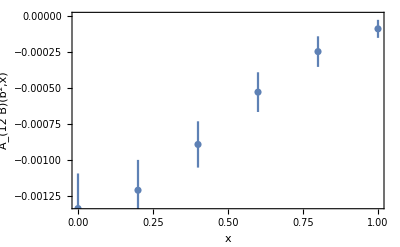

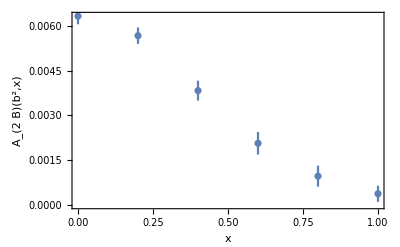

Sivers shift in GeV

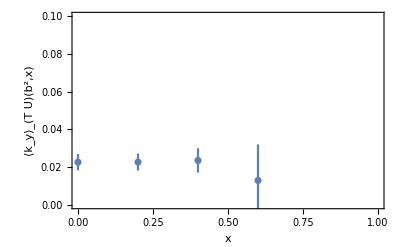

```mathematica
SiversShift2[9,-1, 8]
```

for  are all removed!

Fitting:    -> () = {⟨0.059(41)⟩_(2902J), ⟨-220(230)⟩_(2902J), ⟨-71(33)⟩_(2902J)}, chisquareDoF = 3.37414
 Fitting:    -> () = {⟨0.129(13)⟩_(2902J), ⟨0.072(12)⟩_(2902J), ⟨3.92(79)⟩_(2902J)}, chisquareDoF = 1.30343
 Fitting:   -> () =                                                                                                    3
{⟨-44.2(12)⟩_(2902J), ⟨-534(15)⟩_(2902J), ⟨16.66(45) × 10 ⟩_(2902J)} chisquareDoF = 1023.27
  = 9  = -2 ,eta = 8

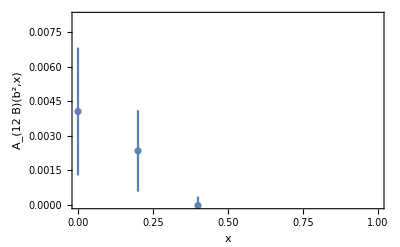

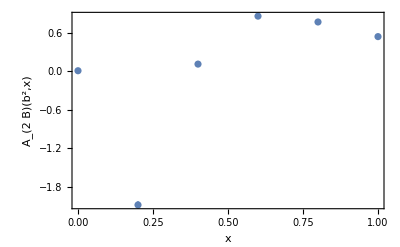

Sivers shift in GeV

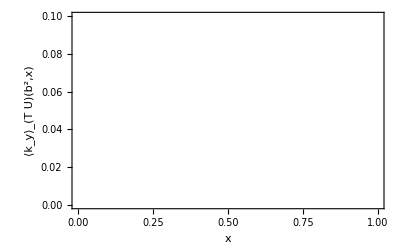

```mathematica
SiversShift2[9,-2, 8]
```

for  are all removed!

Fitting:    -> () =                                                           3
{⟨0.0018(91)⟩_(2902J), ⟨85.3(34) × 10 ⟩_(2902J), ⟨-27(15)⟩_(2902J)}, chisquareDoF = 0.992503
 Fitting:    -> () = {⟨0.43(11)⟩_(2902J), ⟨-2.26(68)⟩_(2902J), ⟨143(41)⟩_(2902J)}, chisquareDoF = 7.7204
 Fitting:   -> () = {⟨-1.45(22)⟩_(2902J), ⟨-25.2(30)⟩_(2902J), ⟨840(87)⟩_(2902J)} chisquareDoF = 68.4312
  = 9  = -3 ,eta = 8

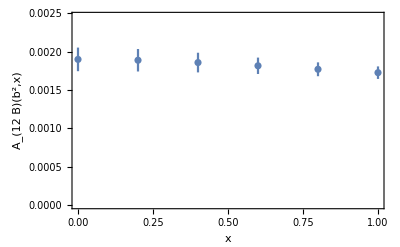

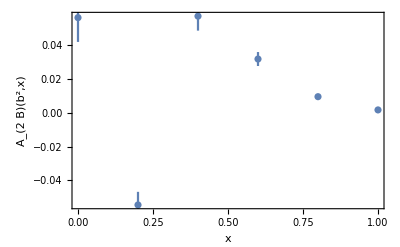

Sivers shift in GeV

-Graphics-

```mathematica
SiversShift2[9,-3, 8]
```

```mathematica
SiversShift3[b2_,P1_, etavalue_]:=Module[{dataforfitA12B, dataforfitA2B, fitJKA12B, fitParasA12B, chisqfitA12B, fitJKA2B, fitParasA2B, chisqfitA2B, fitJKImA2B, fitParasImA2B, chisqfitImA2B},
dataforfitA12B = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->P1,etav->etavalue, bNum->even}],{bL, bT,data}];
dataforfitA2B = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1,etav->etavalue, bNum->even}],{bL, bT,data}];
dataforfitImA2BFull = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1,etav->etavalue, bNum->odd}],{bL, bT,data}];
Print[" for  are all removed!"];
(*dataforfitA12B = Select[dataforfitA12B,Sqrt[#[[1]]^2+#[[2]]^2]>2&];*)
dataforfitA2B = Select[dataforfitA2B,Sqrt[#[[1]]^2+#[[2]]^2]>4&];
dataforfitImA2B = Select[dataforfitImA2BFull,Sqrt[#[[1]]^2+#[[2]]^2]>4&];
modelfitA12B[x1_,x2_,{a_,b_,c_}]:=a*(1/((x1^2)+b))*Exp[(-c*x2^2)];
modelfitA2B[x1_,x2_,{a_,b_,c_}]:=a*(1/((x1^2)+b))*Exp[(-c*x2^2)];
modelfitImA2B[x1_,x2_,{a_,b_,c_}]:=a*x1*(1/((x1^2)+b))*Exp[(-c*x2^2)];
fitJKA12B =JackknifeFit3D[dataforfitA12B,modelfitA12B[bP,bsq,{a,b,c}],{a,b, c},{bP,bsq}, modelfitA12B];
fitParasA12B=FitParameters/. fitJKA12B;
chisqfitA12B=chisquareDoF/. fitJKA12B;
fitJKA2B =JackknifeFit3D[dataforfitA2B,modelfitA2B[bP,bsq,{a,b,c}],{a,b, c},{bP,bsq}, modelfitA2B];
fitParasA2B=FitParameters/. fitJKA2B;
chisqfitA2B=chisquareDoF/. fitJKA2B;
fitJKImA2B =JackknifeFit3D[dataforfitImA2B,modelfitImA2B[bP,bsq,{a,b,c}],{a,b, c},{bP,bsq}, modelfitImA2B];
fitParasImA2B=FitParameters/. fitJKImA2B;
chisqfitImA2B=chisquareDoF/. fitJKImA2B;
Print["Fitting:    -> () = ",OutputForm[fitParasA12B], ", chisquareDoF = ", chisqfitA12B,"\n Fitting:    -> () = ",OutputForm[fitParasA2B], ", chisquareDoF = ", chisqfitA2B, "\n Fitting:   -> () = ",OutputForm[fitParasImA2B]," chisquareDoF = ", chisqfitImA2B, "\n  = ",b2, "  = ",P1," ,eta = ", etavalue];
b2II = b2*fitParasA12B[[1]]/fitParasA12B[[1]];
II= fitParasA12B[[1]]/fitParasA12B[[1]];
fitaA12B =fitParasA12B[[1]];
fitbA12B=fitParasA12B[[2]];
fitcA12B =fitParasA12B[[3]];
fitaA2B =fitParasA2B[[1]];
fitbA2B=fitParasA2B[[2]];
fitcA2B =fitParasA2B[[3]];
fitaImA2B =fitParasImA2B[[1]];
fitbImA2B=fitParasImA2B[[2]];
fitcImA2B =fitParasImA2B[[3]];
MassN = MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B,PL->P1,etav->etavalue, bNum->even}],MN][[1]];
massterm=-MassN[[1]]*(197*0.0001/lata);
siversshiftxforplot={};
fourieA12Bxforplot={};
fourieA2Bxforplot={};
Do[
(*siversrforx = modelfitJackkifex[siversratio,{reducedratio1, fitbA12B, fitbA2B}, x];*)
modelReA12BNfou[pb_, jknum_]:=fitaA12B[[jknum]]*Exp[(-fitbA12B[[jknum]]*((pb^2)/(P1^2)))]*1/(fitcA12B[[jknum]]+(b2^2+((pb^2)/(P1^2))));
modelReA2BNfou[pb_, jknum_]:=fitaA2B[[jknum]]*Exp[(-fitbA2B[[jknum]]*((pb^2)/(P1^2)))]*1/(fitcA2B[[jknum]]+(b2^2+((pb^2)/(P1^2))));
modelImA2BNfou[pb_, jknum_]:=fitaImA2B[[jknum]]*((pb)/(-P1))*Exp[(-fitbImA2B[[jknum]]*((pb^2)/(P1^2)))]*1/(fitcImA2B[[jknum]]+(b2^2+((pb^2)/(P1^2))));
fourierA12Bforx = NFourierTransformJK[modelReA12BNfou,pb,x, Re];
fourierREA2Bforx=NFourierTransformJK[modelReA2BNfou,pb,x, Re];
fourierIMA2Bforx=NFourierTransformJK[modelImA2BNfou,pb,x, Im];
fourierA2Bforx=fourierREA2Bforx-fourierIMA2Bforx;
siversrforx=massterm*fourierA12Bforx/fourierA2Bforx;
AppendTo[siversshiftxforplot,{x,siversrforx}];
AppendTo[fourieA12Bxforplot,{x,fourierA12Bforx}];
AppendTo[fourieA2Bxforplot,{x,fourierA2Bforx}];
,{x,0,1, 0.2}];
MkErrA12B=MakeErrBars[fourieA12Bxforplot];
A12BPltrangMin=(MkErrA12B[[1]][[1]][[2]]+MkErrA12B[[1]][[2]][[1]][[1]])*0.5;
A12BPltrangMax=(MkErrA12B[[1]][[1]][[2]]+MkErrA12B[[1]][[2]][[1]][[2]])*1.2;
PlotfourieA12Bx = ErrorListPlot[MkErrA12B,FrameLabel->{ , }, Frame->True , PlotRange->Full];(* {{Automatic,Automatic},{0,0.0004}}*)
Print[PlotfourieA12Bx];
MkErrA2B=MakeErrBars[fourieA2Bxforplot];
A2BPltrangMin=(MkErrA2B[[1]][[1]][[2]]+MkErrA2B[[1]][[2]][[1]][[1]])*0.5;
A2BPltrangMax=(MkErrA2B[[1]][[1]][[2]]+MkErrA2B[[1]][[2]][[1]][[2]])*2;
PlotfourieA2Bx= ErrorListPlot[MkErrA2B,FrameLabel->{ , }, Frame->True , PlotRange->Full];(*{{Automatic,Automatic},{0.0045,0.0055}}*)
Print[PlotfourieA2Bx];
Print["Sivers shift in GeV"];
MkErrsiversshift=MakeErrBars[siversshiftxforplot];
SsPltrangMin=(MkErrsiversshift[[1]][[1]][[2]]-MkErrsiversshift[[1]][[2]][[1]][[1]])*0.5;
SsPltrangMax=(MkErrsiversshift[[1]][[1]][[2]]-MkErrsiversshift[[1]][[2]][[1]][[2]])*1.2;
Plotsivershift = ErrorListPlot[MkErrsiversshift,FrameLabel->{ , }, Frame->True , PlotRange->{{Automatic,Automatic},{0,0.1}}];(* PlotRange->{{Automatic,Automatic},{-0.3,0}}*)
Print[Plotsivershift];
(*Export["/Users/hariprashadravikumar/Downloads/Lorentz_bL_Gaussian_bT_Fourierx_A12B_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotfourieA12Bx,"PDF",ImageResolution->600];
Export["/Users/hariprashadravikumar/Downloads/Lorentz_bL_Gaussian_bT_Fourierx_A2B_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",PlotfourieA2Bx,"PDF",ImageResolution->600];
Export["/Users/hariprashadravikumar/Downloads/Lorentz_bL_Gaussian_bT_Fourierx_SiversShift_"<>ToString[ampname]<>"_b_"<>ToString[bnum]<>"_P1_"<>ToString[P1]<>"_eta_"<>ToString[etavalue]<>".pdf",Plotsivershift,"PDF",ImageResolution->600];*)
];
```

for  are all removed!

Fitting:    -> () = {⟨-0.125(20)⟩_(2902J), ⟨3.44(69)⟩_(2902J), ⟨0.153(28)⟩_(2902J)}, chisquareDoF = 1.6132
 Fitting:    -> () = {⟨0.2306(96)⟩_(2902J), ⟨5.19(59)⟩_(2902J), ⟨0.0725(41)⟩_(2902J)}, chisquareDoF = 4.76897
 Fitting:   -> () = {⟨0.0134(18)⟩_(2902J), ⟨2.6(14)⟩_(2902J), ⟨0.053(16)⟩_(2902J)} chisquareDoF = 1.30412
  = 9  = -1 ,eta = 8

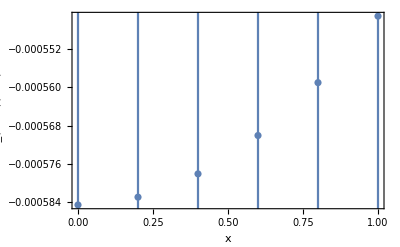

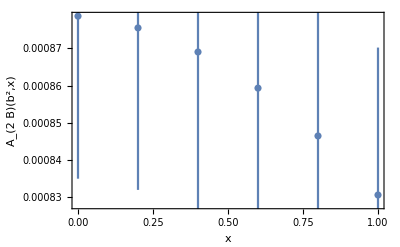

Sivers shift in GeV

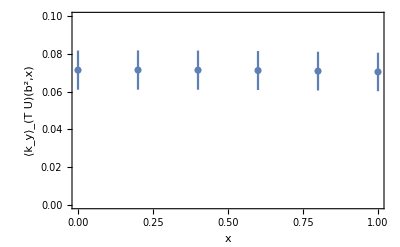

```mathematica
SiversShift3[9,-1, 8]
```

for  are all removed!

Fitting:    -> () = {⟨-0.135(16)⟩_(2902J), ⟨1.61(35)⟩_(2902J), ⟨0.324(58)⟩_(2902J)}, chisquareDoF = 2.6916
 Fitting:    -> () = {⟨0.154(12)⟩_(2902J), ⟨2.85(70)⟩_(2902J), ⟨0.0926(97)⟩_(2902J)}, chisquareDoF = 1.4586
 Fitting:   -> () = {⟨0.0186(29)⟩_(2902J), ⟨2.4(16)⟩_(2902J), ⟨0.061(19)⟩_(2902J)} chisquareDoF = 0.872001
  = 9  = -2 ,eta = 8

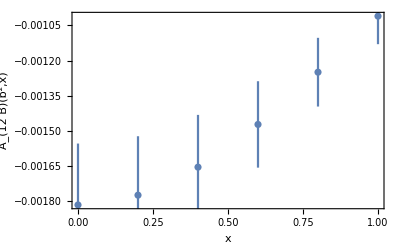

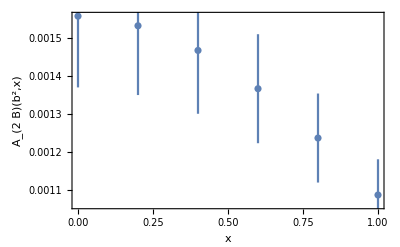

Sivers shift in GeV

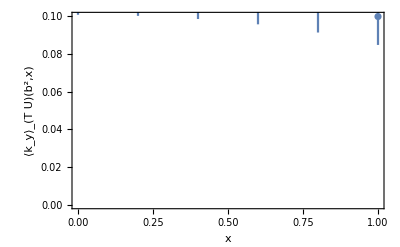

```mathematica
SiversShift3[9,-2, 8]
```

```mathematica
SiversShift3[9,-3, 8]
```